# Dictionary attacks using Wolfram Language

Miguel Angel (Mackaber) Bravo Vidales

## WARNING!!! This essay is only intended to be use for educational purposes, the data presented was obtained from real leaked databases and should be handled with discretion.

So, let’s suppose you suddenly got access to the database of a very popular site, as a Hacker you want to know the passwords of all of their users, but it turns out there isn’t anything in it that looks like passwords, all you have is a bunch of Hexadecimal numbers.

```mathematica
(* Use notebook directory and filename join *)
data =  Import["/Users/mackaber/WSS/Project/Homework/Res/pass_50000.txt","Table","FieldSeparators"-> ":"];
headers = {"hash","freq"};
passwords =Map[ AssociationThread[headers ->#]&,data];
passwords//Dataset
```

Dataset[<>]

## How passwords work?

When you first sign up to a website it usually asks you for a new password for your account, and you have to enter the same password each time you sign in, so... you would assume that this password is compared to the one stored in some kind of database. However, if the password is stored in plaintext it would be very easy for the programmer or anyone that has access to the database (maybe a hacker). Like in the example below, just looking at the code you can realize what the password is.

```mathematica
Panel[DynamicModule[{pass=password},
Column[{InputField[Dynamic[pass]],
Dynamic[If[ToString[pass] === "wolfram",
"Access Granted!",
"Access Denied!"
]]}
]
]]
```

We need some kind of way to check if the password is correct every time is inputted, but storing it without knowing what it originally was. For this we make use of a Hash[] function.
Hash functions are “one-way” functions, this means that we can convert the input to its hash, but we can’t take the hash and convert it back to its input. One of the algorithms used for hashing is known as SHA-1

```mathematica
Hash["wolfram","SHA","HexString"]
```

a84c43b7866a06a6dd4c9d90e813abbd084f752c

This hash is then be stored  in a database,  but then, How do you know a password is correct? Easy!, each time you login the hash function is applied to the input, then its compared to hash stored in the Database, so now, even if the password is leaked the hackers can’t know the password of any account.

Can You Guess the Following password now?

```mathematica
Panel[DynamicModule[{pass=password},
Column[{InputField[Dynamic[pass]],
Dynamic[If[Hash[ToString[pass],"SHA","HexString"] === "7c4a8d09ca3762af61e59520943dc26494f8941b",
"Access Granted!",
"Access Denied!"]
]
}]]]
```

## Dictionary Attacks

Having the passwords hashed in a database  doesn’t necessarily mean we can’t crack the passwords, because as we know, a lot of people in the world may be using something related to them as a password,  as it needs to be something easy to remember, sometimes it may be a common word, a given name or other kind of stuff that can be found in a WordList[]Like the following built-in function

```mathematica
WordList[]//Dataset
```

Dataset[<>]

ThereIf we apply The Hash Function to each one of these words we can have a dictionary to compare our database to!

```mathematica
HashList[wordlist_List] := Map[ AssociationThread[{"word","hash"} ->#]&,{#,ToUpperCase@Hash[#,"SHA","HexString"]}&/@wordlist];
HashList[WordList[]]//Dataset
```

Dataset[<>]

Now that we have our dataset with the most common words, the only thing left to do is to see which of the values appear in the leaked database, and voila!, we have our passwords for the words found in WordList[]

```mathematica
DictionaryAttack[dict_List,dataset_]:= JoinAcross[HashList[dict],dataset,Key["hash"]]
DictionaryAttack[WordList[],passwords]//Dataset
```

Dataset[<>]

What we just have done is known as a Dictionary Attack, and is used by Cybersecurity professionals to audit password databases (and is also used by some malicious hackers).

## Weak passwords

As you may have noticed, I was cheating a little, because the database we are working with doesn’t include usernames, and instead has a field called “freq” which stands for Frequency, which is the number of a password appearing in this database, that’s because I got it from https://haveibeenpwned.com/ which has compiled this database from different security breaches, and hashing the passwords as some of them contained sensitive information.

The main purpose of this site is inform people to stop using weak passwords that are vulnerable to dictionary attacks, the list we obtained is useful to know which passwords are the most used and therefore most insecure, but having it doesn’t make it very easy to read, so the message could be better understood by using a WordCloud[]

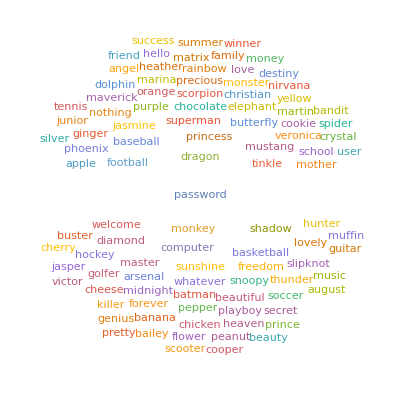

```mathematica
PasswordCloud[list_List,dataset_:passwords] := WordCloud[<|#word->ToExpression[#freq]&/@ DictionaryAttack[list,dataset]|>]
PasswordCloud[WordList[],passwords]
```

This looks good but we can make it look better, so the message gets straight away

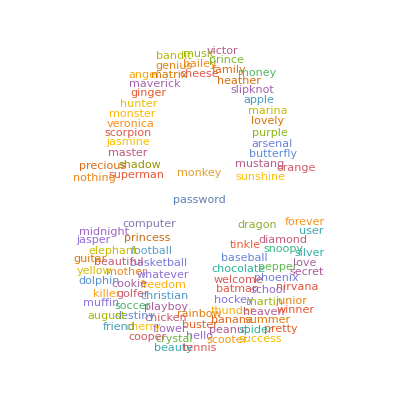

Transpose::nmtx: The first two levels of {1,2,3,4,5,6} cannot be transposed.

Transpose[{1,2,3,4,5,6}]

```mathematica
PasswordCloud[list_List,dataset_,mask_] := WordCloud[<|#["word"]->ToExpression[#["freq"]]&/@ DictionaryAttack[list,dataset]|>,ColorNegate[mask]]
PasswordCloud[WordList[],passwords,-Graphics-]
```

Now, Let’s Try other stuff, like Country names, using The Free form input

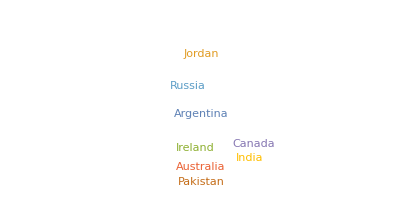

```mathematica
countries = EntityList[EntityClass["Country","Countries"]]//CommonName;
PasswordCloud[countries,passwords]
```

What about number sequences?

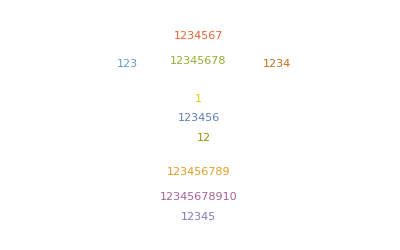

```mathematica
sequences = StringJoin/@Table[ToString/@Range[n],{n,10}];
PasswordCloud[sequences,passwords]
```

Even Football Teams!

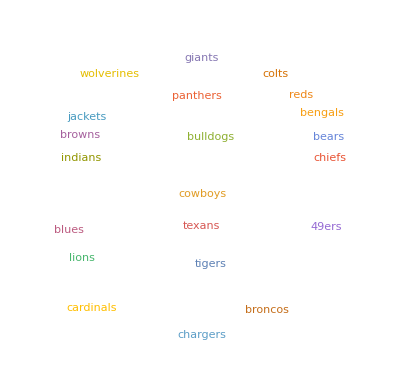

```mathematica
teams = #[[-1]]&/@StringSplit@WolframAlpha["Football Teams",{{"Result",1},"ComputableData"},PodStates->{"Result__More"}]//Decapitalize;
PasswordCloud[teams,passwords]
```

```mathematica
layouts = Join[
StringTake["qwertyuiop",#]&/@Range[10],
StringTake["asdfghjkl",#]&/@Range[9],
StringTake["zxcvbnm",#]&/@Range[7]
];
PasswordCloud[layouts,passwords]
```

PasswordCloud[{q,qw,qwe,qwer,qwert,qwerty,qwertyu,qwertyui,qwertyuio,qwertyuiop,a,as,asd,asdf,asdfg,asdfgh,asdfghj,asdfghjk,asdfghjkl,z,zx,zxc,zxcv,zxcvb,zxcvbn,zxcvbnm},{<|hash→7C4A8D09CA3762AF61E59520943DC26494F8941B,freq→23174662|>,<|hash→F7C3BC1D808E04732ADF679965CCC34CA7AE3441,freq→7671364|>,49996,<|hash→4F09C6D977B30BF4762B0481F8487A9DF0948B35,freq→3402|>,<|hash→ADBC4698B1F9B90AA36DB45E59EC184B44B981DA,freq→3402|>}]
 |  |  |  |

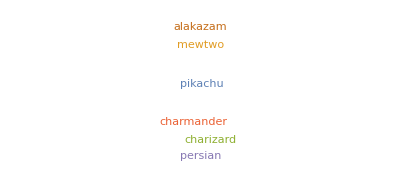

```mathematica
pokemons = EntityList[EntityClass["Pokemon",All]]//CommonName//Decapitalize;
PasswordCloud[pokemons,passwords]
```

Finally, Let’s compare it with all the previous lists for comparison

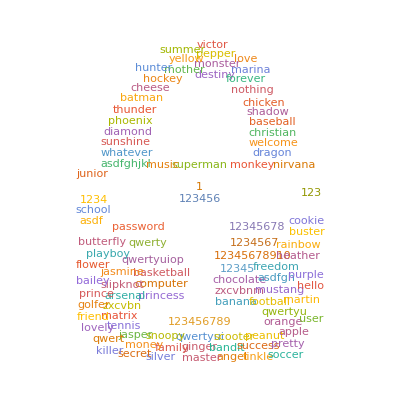

```mathematica
all = Union[WordList[],countries,sequences,teams,layouts,pokemons];
PasswordCloud[all,passwords,-Graphics-]
```